```mathematica
Exit[]
```

```mathematica
BS[s_,SK_,r_,T_]:=SK CDF[NormalDistribution[],d[SK,s,r,T]]-Exp[-r T]CDF[NormalDistribution[],d[SK,s,r,T]-s Sqrt[T]];d[sk_,s_,r_,T_]:=(Log[sk]+(r+s^2/2)T)/s/Sqrt[T]
Preis[Startkapital_, Gewinnschwelle_,Sigma_, Laufzeit_,r_]:=Gewinnschwelle*BS[Sigma,Startkapital/Gewinnschwelle,r,Laufzeit];
D[Preis[p,G,s,T,r],p];
Delta[p_,G_,s_,T_,r_]:=G ((ⅇ^(-(((r+s^2/2) T+Log[p/G])^2)/(2 s^2 T)))/(G √(2 π) s √T)-(ⅇ^(-r T-1/2 (-s √T+((r+s^2/2) T+Log[p/G])/(s √T))^2))/(p √(2 π) s √T)+(1+Erf[((r+s^2/2) T+Log[p/G])/(√2 s √T)])/(2 G))
```

```mathematica
D[Delta[p,G,s,T,r]q p/S,p]
```

```mathematica
Gam[p_,G_,s_,T_,r_]:=G ((ⅇ^(-(((r+s^2/2) T+Log[p/G])^2)/(2 s^2 T)))/(G √(2 π) s √T)-(ⅇ^(-r T-1/2 (-s √T+((r+s^2/2) T+Log[p/G])/(s √T))^2))/(p √(2 π) s √T)+(1+Erf[((r+s^2/2) T+Log[p/G])/(√2 s √T)])/(2 G))+G p ((ⅇ^(-r T-1/2 (-s √T+((r+s^2/2) T+Log[p/G])/(s √T))^2))/(p^2 √(2 π) s √T)+(ⅇ^(-(((r+s^2/2) T+Log[p/G])^2)/(2 s^2 T)))/(G p √(2 π) s √T)-(ⅇ^(-(((r+s^2/2) T+Log[p/G])^2)/(2 s^2 T)) ((r+s^2/2) T+Log[p/G]))/(G p √(2 π) s^3 T^(3/2))+(ⅇ^(-r T-1/2 (-s √T+((r+s^2/2) T+Log[p/G])/(s √T))^2) (-s √T+((r+s^2/2) T+Log[p/G])/(s √T)))/(p^2 √(2 π) s^2 T))
```

## Processes (real-world, non-risk-neutral)

```mathematica
$Assumptions=dt^2==0&&dt*dW==0&&dW^2==dt&&S>0&&M>0&&s>0;

dS = α S dt + σ S dW; (*Aktie*)
dP = r (P - q*P) dt + q P/S dS; (*Kundenportfolio mit Zins r*)
  dX = Δ dS + r (X - Δ S) dt;(*Heding portfolio*)
Δ = q D[V[P, t], P];(*Heding rule*)

dLogP =Simplify[dP/P-1/2 dP^2/P^2](*LogKundenportfolio mit Zins r*)
Simplify[dX]
```

dW q σ+dt (r-q r+q α-(q^2 σ^2)/2)

dt r X+q S (dt (-r+α)+dW σ) V^(1,0)[P,t]

## Hedging Simulation:

0.00273973

{0.016,Null}

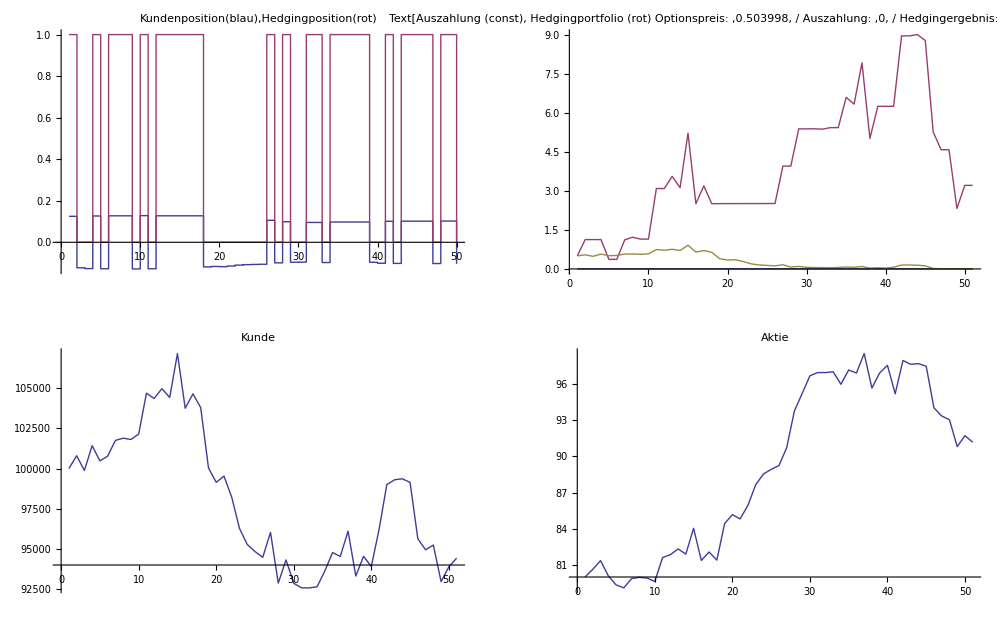

```mathematica
P0=10;M=10;S0=80;
σ=0.3;(*Volaitlität*)
r=0.09;(*risk-free Zinssatz*)
T=50/365;(*Laufzeit in jahren*)
α=0.2;(*Stock drift*)
K=1;(*Hedges täglich*)
nt=Ceiling[365 T ]K;dt=N[T/nt]
n=1;(*MonteCarlo Durchläufe*)



(*Kunde2*)qk=RandomReal[{-1,1},{nt/K}];
(*schlimmster Kunde*)qk=Table[1,{nt/K}];
(*Kunde3*)qk=RandomInteger[{0,1},{nt/K}];
(*schlimmster Kunde*)qk=2*RandomInteger[{0,1},{nt/K}]-1;

dW=RandomReal[NormalDistribution[],{nt n}]Sqrt[dt];
Timing[
PE=0;PV=0;

(*MonteCarlo Loop*)
For[j=0,j<n,j++,

P=Log[P0];W=0;S=S0;s={S0};p={P0 10000};X=Preis[P0,M,σ,T,r];x={X};h={};v={};Q={};

(*Time loop*)
For[i=1,i<nt+1,i++,
AppendTo[v,Preis[Exp[P],M,σ,T-dt*(i-1),r]];
W+=dW[[i]];(*Brownian Motion*)
dS=Exp[(α-σ^2/2) i dt+σ W]S0-S;(*Stock price Increment*)
q=qk[[Ceiling[i/K]]] ;
H=Ceiling[q Exp[P]/S  Delta[Exp[P],M,σ,T-dt*(i-1),r]];(*new Hedgingposition*)
X+=dt r X+H S (dt (-r+α)+dW[[i]] σ) ;(*new Hedgingportfolio*)
P+=dW[[i]] q σ+dt q ( α-q σ^2/2);(*new Portfolio*)



S+=dS;(*new Stockprice*)

AppendTo[Q,q Exp[P]/S];
AppendTo[s,S];
AppendTo[p,Exp[P]10000];
AppendTo[x,X];

AppendTo[h,H];

]
(*PE+=Max[Exp[P]*P0-M,0];PV+=Max[Exp[P]*P0-M,0]^2;{"Mean:", Exp[-r T]PE/n,"2 StD of Mean:",2 Sqrt[Exp[-2r T]/n/(n-1)(PV-PE^2/n)]}*)
];]
AppendTo[v,Max[p[[nt+1]]/10000-M,0]];
Ausz=Max[p[[nt+1]]/10000-M,0];Print[""];GraphicsGrid[{{ListLinePlot[{Q,h},InterpolationOrder->0,PlotLabel->Text["Kundenposition(blau),Hedgingposition(rot)"]],ListLinePlot[{Ausz&/@x,x,v},InterpolationOrder->1,PlotRange->All,PlotLabel->Text["Auszahlung (const), Hedgingportfolio (rot)
Optionspreis: ",x[[1]]," / Auszahlung: ",Ausz," / Hedgingergebnis: ",x[[nt+1]],"
Kosten: ",x[[1]]+Ausz-x[[nt+1]]]]},{ListLinePlot[{p},InterpolationOrder->1,PlotLabel->Text["Kunde"]],ListLinePlot[{s},InterpolationOrder->1,PlotLabel->Text["Aktie"]]}},ImageSize->1000]
```

```mathematica
Total[Abs[Differences[h]]]+h[[1]]+h[[nt]]
Length[h]
```

90.5624

50

```mathematica
P0=10;M=10;S0=6;
σ=0.3;(*Volaitlität*)
r=0.09;(*risk-free Zinssatz*)
T=1/12;(*Laufzeit in jahren*)
α=1.2;(*Stock drift*)
K=1;(*Hedges täglich*)
nt=Ceiling[365 T ]K;dt=N[T/nt];
n=10000;(*MonteCarlo Durchläufe beeinflussen die Genauigkeit des ergebnisses*)

(*Kunde2*)qk=RandomReal[{-1,1},{nt/K}];
(*Kunde3*)qk=RandomInteger[{0,1},{nt/K}];
(*schlimmster Kunde*)qk=2*RandomInteger[{0,1},{nt/K}]-1;
(*schlimmster Kunde*)qk=Table[1,{nt/K}];

dW=RandomReal[NormalDistribution[],{nt n}]Sqrt[dt];

Timing[
PE=0;PV=0;PVV=0;PVVV=0;pe={};

(*MonteCarlo Loop*)
For[j=0,j<n,j++,

P=Log[P0];W=0;S=S0;X=Preis[P0,M,σ,T,r];

(*Time loop*)
For[i=1,i<nt+1,i++,

W+=dW[[i+j nt]];(*Brownian Motion*)
dS=Exp[(α-σ^2/2) i dt+σ W]S0-S;(*Stock price Increment*)
q=qk[[Ceiling[i/K]]];
H=q Exp[P]/S  Delta[Exp[P],M,σ,T-dt*(i-1),r];(*new Hedgingposition*)
X+=dt r X+H S  (dt (-r+α)+dW[[i+j nt]] σ) ;(*new Hedgingportfolio*)
P+=dW[[i+j nt]] q σ+dt q ( α-q σ^2/2);(*new Portfolio*)
S+=dS;(*new Stockprice*)
];

AppendTo[pe,X-Max[Exp[P]-M,0]];
PE+=X-Max[Exp[P]-M,0];PV+=(Max[Exp[P]-M,0]-X)^2;PVV+=(-Max[Exp[P]-M,0]+X)^3;PVVV+=(Max[Exp[P]-M,0]-X)^4]
Print["Option Price:       ",Preis[P0,M,σ,T,r]];
Print["Hedgegewinn:        ", Exp[-r T]PE/n," (Error", Exp[-r T] Sqrt[1/n/(n-1)(PV-PE^2/n)],")"];
Print["2 StandardDeviations:  ",2 Exp[-r T]Sqrt[1/(n-1)(PV-PE^2/n)],"  (Error ",2 Exp[-r T]Sqrt[Sqrt[(PVVV-4 PVV PE/n+6 PV PE^2/n^2-3PE^4/n^3)/(n-1)]/n]," ⧦ ",100Sqrt[Sqrt[(PVVV-4 PVV PE/n+6 PV PE^2/n^2-3PE^4/n^3)/(n-1)]/n]/Sqrt[1/(n-1)(PV-PE^2/n)],"%)"];
Print["Shortfall(Verlust)wahrscheinlichkeit:        ", N[Length[Select[pe,#<0&]]/n 100]," %"];
Print["(Error verringern durch höhreres n)"];
]
Histogram[pe,Automatic,"ProbabilityDensity",Epilog->First@Plot[ PDF[NormalDistribution[Exp[-r T]PE/n,Exp[-r T]Sqrt[1/(n-1)(PV-PE^2/n)]],x],{x,-4,4},PlotStyle->Red],PlotRange->All]
```

Option Price:       0.382744

Hedgegewinn:        -0.00551279 (Error0.000509853)

2 StandardDeviations:  0.101971  (Error 0.00147121 ⧦ 1.44278%)

Shortfall(Verlust)wahrscheinlichkeit:        55.38 %

(Error verringern durch höhreres n)

{23.649,Null}

-Graphics-

```mathematica
P2-P
```

0.